## Управление процессом интегрирования

## Интегрированные математические пакеты

Юдинцев В. В.

Кафедра теоретической механики. Самарский университет.

## Остановка процесса интегрирования при выполнении условия

### Определение момента падения на землю точки, движущейся по баллистической траектории

#### Уравнения движения точки в плоскости в однородном поле силы тяжести

```mathematica
eq={x''[t]==0,y''[t]==-g };
```

#### Начальные условия

```mathematica
ic={x[0]==0,y[0]==0,x'[0]==Subscript[V, 0] Cos[Subscript[φ, 0]],y'[0]==Subscript[V, 0] Sin[Subscript[φ, 0]]};
```

#### Параметры

```mathematica
p={g->9.81,Subscript[V, 0]->10,Subscript[φ, 0]->45°};
```

```mathematica
sol=NDSolve[{eq,ic}//.p,{x[t],y[t],x'[t],y'[t]},{t,0,2}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t]}}

#### Траектория точки

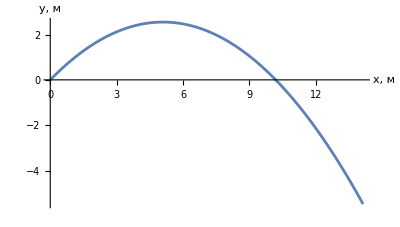

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,2},AxesLabel->{"x, м","y, м"}]
```

Траектория продолжилась и при y<0.
Как остановить процесс интегрирования при достижении нулевой высоты?
WhenEvent[условие, что делать]
или
WhenEvent[условие, {что делать,что делать,что делать,что делать}]

```mathematica
sol2=NDSolve[
{
eq,
ic,
WhenEvent[y[t]<0,"StopIntegration"]
}//.p,
{x[t],y[t],x'[t],y'[t]},{t,0,2}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t]}}

Процесс интегрирования остановился при t = 1.44 c, в момент достижения нулевой высоты.

Время остановки извлекается из решения

```mathematica
sol2[[1,1]]
```

x[t]→InterpolatingFunction[…][t]

```mathematica
sol2[[1,1,2]]
```

InterpolatingFunction[…][t]

```mathematica
sol2[[1,1,2,0]]
```

InterpolatingFunction[…]

```mathematica
sol2[[1,1,2,0,1]]
```

{{0.,1.4416}}

```mathematica
sol2[[1,1,2,0,1,1,2]]
```

1.4416

```mathematica
tk=sol2[[1,1,2,0,1,1,2]];
```

#### Траектория точки до момента падения на землю

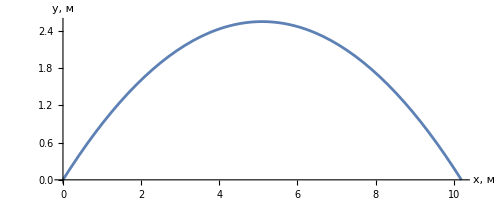

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,tk},AxesLabel->{"x, м","y, м"}]
```

Условие можно задать функцией, которая вычисляется только для аргумента-числа:

```mathematica
h0Event[x_?NumericQ]:=x<0;
```

```mathematica
sol2=NDSolve[
{
eq,
ic,
WhenEvent[h0Event[y[t]],"StopIntegration"]
}//.p,
{x[t],y[t],x'[t],y'[t]},{t,0,2}];
```

## Изменение динамических переменных

### Отскок от земли

```mathematica
h0Event[x_?NumericQ]:=x<0;
```

При достижении нулевой высоты (ударе о землю) меняем направление вертикальной скорости на противоположное с коэффициентом меньше 1, т.е. моделируем мгновенный отскок с потерей кинетической энергии

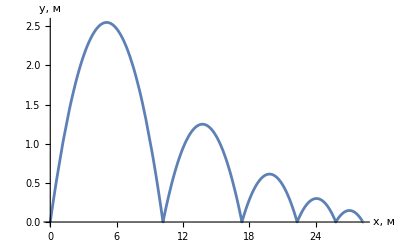

```mathematica
sol=NDSolve[
{
eq,
ic,
WhenEvent[h0Event[y[t]],y'[t]->-0.7y'[t]]
}//.p,
{x[t],y[t],x'[t],y'[t]},{t,0,4}];
ParametricPlot[{x[t],y[t]}/.sol,{t,0,4},AspectRatio->1/GoldenRatio,AxesLabel->{"x, м","y, м"}]
```

### Сохраняем координаты x точек падения

Введем в уравнение еще одну переменную c[t], значение которой будет увеличивать на 1 при регистрации события. Эта переменная дискретная и будет изменяться скачкообразно (увеличиваться на 1) при наступлении события y<0. Переменная c[t] включается в список динамических переменных функции NDSolve, а также при помощи параметра DiscreteVariables указывается, что эта переменная  является дискретной.

```mathematica
h0Event[q_?NumericQ]:=q<0;
```

```mathematica
sol=NDSolve[
{
eq,
ic,c[0]==0,
WhenEvent[h0Event[y[t]],{y'[t]->-0.7y'[t],c[t]->x[t]}]
}//.p,
{x[t],y[t],x'[t],y'[t],c[t]},{t,0,10},DiscreteVariables->c[t]];
```

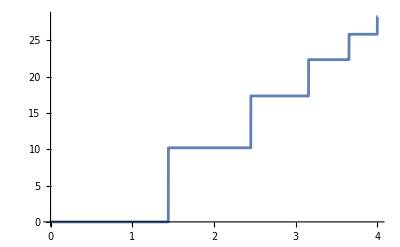

```mathematica
Plot[c[t]/.sol,{t,0,4}]
```

Функция c[t] будет скачкообразно изменяться до значения координаты х точки падения тела.

## Включение

Предположим, что тело падает на деформируемую поверхность и при y < 0 на тело начинает действовать “выталкивающая” сила упругости, которая возникает при деформации поверхности. Предположим также, что эта сила пропорциональная глубине δ = -y и скорости деформации dδ/dt и направлена вверх:
Fn = k1*δ + k2*(dδ/dt)

#### Уравнения

В уравнение для y добавим силу Fn, которую умножим на дискретную переменную c[t],   принимающую значения 1 или 0 (1 если y<0).

```mathematica
eq={x''[t]==0,y''[t]==-g +c[t]*Fn/m};
```

#### Начальные условия

```mathematica
ic={x[0]==0,y[0]==0,x'[0]==Subscript[V, 0] Cos[Subscript[φ, 0]],y'[0]==Subscript[V, 0] Sin[Subscript[φ, 0]]};
```

#### Параметры

К списку параметров добавим массу, выражение для силы Fn, а также коэффициенты жесткости и демпфирования поверхности:

```mathematica
p={g->9.81,Subscript[V, 0]->10,Subscript[φ, 0]->45°,k1->300,k2->10,m->1,Fn->k1(-y[t])+k2(-y'[t])};
```

Для функции NDSolve укажем два события y<0 и y>0, при регистрации которых будет изменять значение дискретной переменной c[t] (признак действия силы Fn):

```mathematica
sol=NDSolve[
{
eq,
ic,c[0]==0,
WhenEvent[y[t]<0,{c[t]->1}],
WhenEvent[y[t]>0,{c[t]->0}]
}//.p,
{x[t],y[t],x'[t],y'[t],c[t]},{t,0,10},DiscreteVariables->c[t]];
```

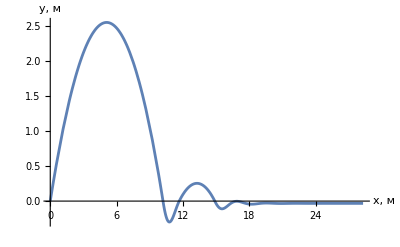

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,4},AspectRatio->1/GoldenRatio,AxesLabel->{"x, м","y, м"}]
```

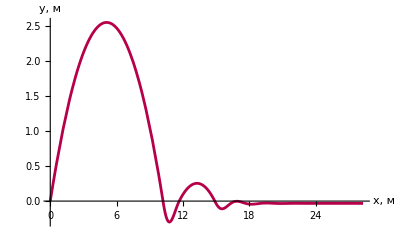

```mathematica
ParametricPlot[{x[t],y[t]}/.sol,{t,0,4},AspectRatio->1/GoldenRatio,AxesLabel->{"x, м","y, м"},ColorFunction->Function[{x,y},If[y<0,Red,Blue]],ColorFunctionScaling->False]
```

## Функции Sow и Reap

Функции Sow (“засевать”) и Reap (“собирать урожай”) используются для сбора результатов вычислений.
Далее Sow используется для сохранения значения x[t] при наступлении события y[t]<0 после изменения знака вертикальной скорости. Чтобы результаты “посева” используется Reap, аргументом которой является выражение, в котором происходит “посев”. Функция Reap возвращает результат работы функции NDSlove и результаты “посева”, т.е. значения x[t] в момент наступления событий y[t]<0.

#### Уравнения

```mathematica
eq={x''[t]==0,y''[t]==-g };
```

#### Начальные условия

```mathematica
ic={x[0]==0,y[0]==0,x'[0]==Subscript[V, 0] Cos[Subscript[φ, 0]],y'[0]==Subscript[V, 0] Sin[Subscript[φ, 0]]};
```

#### Параметры

```mathematica
p={g->9.81,Subscript[V, 0]->10,Subscript[φ, 0]->45°};
```

```mathematica
sol=Reap[NDSolve[
{
eq,
ic,c[0]==0,
WhenEvent[h0Event[y[t]],{y'[t]->-0.7y'[t],Sow[x[t]]}]
}//.p,
{x[t],y[t],x'[t],y'[t]},{t,0,4}]]
```

{{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t]}},{{10.1937,17.3293,22.3242,25.8206,28.2681}}}

#### Решение дифференциального уравнения

```mathematica
sol[[1]]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t]}}

#### Сохраненные функцией Sow результаты

```mathematica
sol[[2]]
```

{{10.1937,17.3293,22.3242,25.8206,28.2681}}

## Сечения Пуанкаре

В теории динамических систем, разделе математики, отображение Пуанкаре (также отображение последования, отображение первого возвращения) — это проекция некоторой площадки в фазовом пространстве на себя (или на другую площадку) вдоль траекторий (фазовых кривых) системы.
https://ru.ruwiki.ru/wiki/Отображение_Пуанкаре

### Уравнение Дуффинга

```mathematica
eq=x''[t]+δ x'[t]+α x[t]+β x[t]^3==γ Cos[ω t];
p={α->-1,β->0.25,δ->0.1,γ->2.5,ω->2};

sol=NDSolve[{eq,x[0]==0,x'[0]==0}/.p,{x[t],x'[t]},{t,0,100}];
```

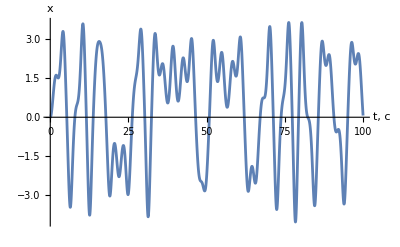

```mathematica
Plot[x[t]/.sol,{t,0,100},AxesLabel->{"t, c","x"}]
```

#### Фазовый портрет

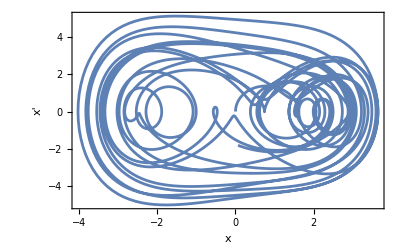

```mathematica
ParametricPlot[{x[t],x'[t]}/.sol,{t,0,100},AspectRatio->1/GoldenRatio,Frame->True,AxesLabel->{"x","x'"}]
```

Сохраним пары координат точки в фазовом пространстве (x[t], x’[t]) в моменты времени, когда время кратно 2 π/ω и покажем эти точки на графике. 

WhenEvent[Mod[t,2 π/ω],Sow[{x[t],x'[t]}]]

```mathematica
solp=Reap[NDSolve[{eq,x[0]==0,x'[0]==0,WhenEvent[Mod[t,2 π/ω],Sow[{x[t],x'[t]}]]}/.p,{x[t],x'[t]},{t,0,20000}]];
```

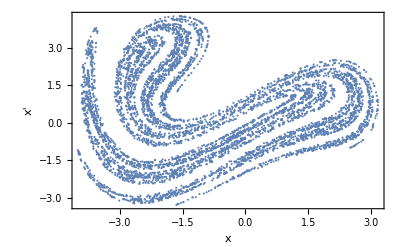

```mathematica
ListPlot[solp[[2,1]],Frame->True,AxesLabel->{"x","x'"}]
```